#### 多重积分

```mathematica
Integrate[1, {x, -Pi, Pi}, {y, -Pi, Pi}, {z, -Pi, Pi}]
```

8 π^3

#### 求导

```mathematica
D[x^3, x]
```

3 x^2

#### 高阶求导

```mathematica
D[x^3, {x, 2}]
```

6 x

#### 复合函数求偏导

```mathematica
D[x^2 + x*y^2 + y, x, y]
```

2 y

#### 求极值

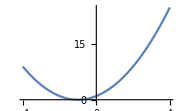

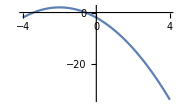

{0.,{x→-1.}}

{2.,{x→-2.}}

```mathematica
Plot[x^2 + 2*x + 1 == 0, {x, -4, 4}, ImageSize -> Small]
Plot[-x^2 - 4*x - 2 == 0, {x, -4, 4}, ImageSize -> Small]
FindMinimum[x^2 + 2*x + 1, x]
FindMaximum[-x^2 - 4*x - 2, x]
```

#### 条件极值

```mathematica
FindMaximum[{x^2, 0 <= x <= 5}, x]
```

{25.,{x→5.}}